## VQE analysis and plots for the chemistry-stuff paper

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Set the chemical accuracy!

```mathematica
chemacc=1.59*10^-3
```

0.00159

## Modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit (Daniel's format). Returns {hamiltonian, nterms, nqubits}.";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->Subscript[Id, 0] a};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

SetAttributes[PrintTables,HoldRest]
PrintTables[molecule_,data_]:=With[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
trial=1;
disp=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
res⟦3⟧,
ϵgs<=chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦4⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp,{"trial","runtime(min)","chemacc?","ϵgs","ngates", "elims","fevs","ngates/cycle","aborted cycle"}];
DestroyAllQuregs[];
Print@TextGrid[disp,Frame->All]
]

GetSuccData[molecule_]:=Module[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule],
filtered={}
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
If[ϵgs<=chemacc, AppendTo[filtered,res]]
,{res,results}];
DestroyAllQuregs[];
filtered
]
```

```mathematica
CountGates::usage="CountGates[circuit], return the count for {doubles, singles}";
CountGates[circuit_]:=Module[{doubles},
doubles=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{doubles,Length@circuit-doubles}
]
```

## Load results, hamiltonians, labels, groundstate,occupations

```mathematica
SetDirectory["~/chemistry-code/vqe/hamiltonians"];
hamiltonians=<|"BeH2"->FormatHamiltonian["hamiltonian-beh2.txt"],"LiH"->FormatHamiltonian["hamiltonian-lih.txt"],"H2O"->FormatHamiltonian["hamiltonian-h2o.txt"],"H2"->FormatHamiltonian["hamiltonian-h2.txt"],"H3"->FormatHamiltonian["hamiltonian-h3.txt"],
"H4"->FormatHamiltonian["hamiltonian-h4.txt"],"He2H"->FormatHamiltonian["hamiltonian-he2h.txt"],"He3H"->FormatHamiltonian["hamiltonian-he3h.txt"]|>;
labels=<|"BeH2"->"BeH_2","LiH"->"LiH","H2O"->"H_2O","H2"->"H_2","H4"->"H_4","H3"->"H_3","He2H"->TraditionalForm["He_2H^+"],"He3H"->TraditionalForm@"He_3H^+"|>;
groundstates=<|"H2O"->-75.01402200471308,"LiH"->-7.882059857867098,"H2"->-1.1372838344885023,"H4"->-1.9961503255188098,"He2H"->-5.769926974270885,"He3H"->-8.575314719616504,"BeH2"->-15.5951755114264,"H3"->-1.4198925029235445|>;
occupations=<|"BeH2"->6,"LiH"->4,"H2O"->10,"H2"->2,"H3"->3,"H4"->4,"He2H"->5,"He3H"->7|>;
```

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}

```mathematica
SetDirectory["~/chemistry-code/vqe/results"];
resBeH2<<resBeH2.mx;
resLiH<<resLiH.mx;
resH2O<<resH2O.mx;
resH2<<resH2.mx;
resH4<<resH4.mx;
resH3<<resH3.mx;
resHe3H<<resHe3H.mx;
resHe2H<<resHe2H.mx;
data=<||>;
data["BeH2"]=resBeH2;
data["LiH"]=resLiH;
data["H2O"]=resH2O;
data["H2"]=resH2;
data["H4"]=resH4;
data["H3"]=resH3;
data["He2H"]=resHe2H;
data["He3H"]=resHe3H;
```

```mathematica
resH2[[1]]
```

{{Rx_2[θ_38],C_2[Ry_0[θ_34]],C_0[Rx_1[θ_7]],C_1[Rz_3[θ_21]],C_2[Ry_3[θ_19]],C_0[Rx_1[θ_16]],C_2[Ry_1[θ_6]]},<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>,2.64941,<|ansatz→{{},{Rx_2[θ_38],C_2[Ry_0[θ_34]],C_0[Rx_1[θ_7]],C_1[Rz_3[θ_21]],C_2[Ry_3[θ_19]],C_0[Rx_1[θ_16]],C_2[Ry_1[θ_6]]},{Rx_2[θ_38],C_2[Ry_0[θ_34]],C_0[Rx_1[θ_7]],C_1[Rz_3[θ_21]],C_2[Ry_3[θ_19]],C_0[Rx_1[θ_16]],C_2[Ry_1[θ_6]]}},θvars→{<||>,<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>,<|θ_6→3.14159,θ_7→3.1416,θ_16→-3.14159,θ_19→-3.14159,θ_21→3.14147,θ_34→-3.14159,θ_38→0.225563|>},E→{-1.11676,-1.13728,-1.13728},idx→{1,41,41}|>,1802,{2,3},{0,6,3,23}}

## Tables

### Full results

Table[Print[labels[mol]]; PrintTables[mol, data], {mol, Keys@hamiltonians}];

BeH_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 446.065 | True | 0.000786197 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {}
2 | 228.247 | True | 0.00109689 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {}
3 | 471.871 | True | 0.000669187 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {}
4 | 35.3696 | True | 0.000891144 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {}
5 | 743.145 | True | 0.000997642 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {}
6 | 415.241 | False | 0.00310257 | 74 | {4, 1, 255, 764} | 55246 | {0, 21, 22, 27, 44, 42, 43, 47, 35, 48, 55, 74, 74} | {}
7 | 269.037 | True | 0.00107556 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {2}
8 | 297.075 | True | 0.00107872 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {}
9 | 486.603 | True | 0.000668278 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {}
10 | 55.8 | False | 0.017846 | 18 | {0, 0, 66, 172} | 6159 | {0, 7, 13, 18, 18} | {}

LiH

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 59.2913 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {}
2 | 23.8022 | False | 0.0040206 | 12 | {0, 28, 29, 81} | 2938 | {0, 10, 12, 12} | {4}
3 | 82.2815 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {9}
4 | 6.86707 | False | 0.0207014 | 0 | {0, 0, 0, 0} | 785 | {0, 0} | {1, 2}
5 | 13.9845 | False | 0.00402039 | 8 | {1, 25, 0, 66} | 1801 | {0, 8, 8} | {2}
6 | 64.0422 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {}
7 | 53.7304 | False | 0.00160868 | 17 | {1, 98, 100, 64} | 6754 | {0, 8, 10, 15, 17, 17} | {}
8 | 25.1661 | False | 0.00401906 | 9 | {0, 43, 53, 45} | 3172 | {0, 7, 9, 9} | {}
9 | 277.232 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {}
10 | 94.1075 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {}

H_2O

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 60 x | True | 0.0015335 | 86 | {0, 0, 167, 905} | 97633 | {0, 20, 24, 36, 39, 44, 49, 59, 68, 73, 76, 75, 79, 89, 86, 86} | {}
2 | 1506.21 | False | 0.00171029 | 96 | {1, 1, 237, 1038} | 92652 | {0, 7, 11, 13, 15, 27, 35, 39, 48, 47, 51, 52, 57, 65, 73, 79, 85, 96, 96} | {}
3 | 2418.44 | True | 0.0014174 | 103 | {2, 0, 198, 1255} | 129132 | {0, 24, 34, 32, 35, 42, 42, 52, 58, 58, 65, 78, 90, 83, 90, 97, 103, 103} | {}
4 | 1981.21 | False | 0.00175573 | 119 | {1, 1, 88, 1209} | 104850 | {0, 14, 26, 29, 33, 32, 41, 45, 53, 56, 67, 68, 87, 98, 109, 119, 119} | {}
5 | 1360.8 | False | 0.0026217 | 85 | {0, 0, 93, 971} | 79204 | {0, 7, 22, 28, 39, 41, 48, 54, 65, 77, 70, 75, 85, 85} | {}
6 | 1235.63 | False | 0.00159058 | 88 | {1, 0, 182, 860} | 76320 | {0, 6, 11, 17, 26, 29, 40, 45, 57, 69, 62, 65, 68, 80, 88, 88} | {}
7 | 218.536 | False | 0.0208635 | 34 | {0, 0, 35, 267} | 16349 | {0, 21, 25, 27, 34, 34} | {}
8 | 750.734 | False | 0.012768 | 59 | {0, 0, 148, 682} | 50403 | {0, 6, 13, 19, 25, 30, 35, 39, 44, 53, 57, 59, 59} | {}
9 | 1780.96 | True | 0.000575987 | 98 | {1, 0, 186, 1159} | 106765 | {0, 7, 17, 20, 25, 35, 32, 37, 40, 43, 58, 63, 72, 79, 82, 88, 79, 91, 98, 98} | {}
10 | 1598.03 | False | 0.0113934 | 84 | {1, 1, 0, 1163} | 90004 | {0, 40, 22, 27, 38, 43, 44, 54, 58, 71, 75, 82, 80, 84, 84} | {16, 17}
11 | 94.1075 | False | 0.0128035 | 54 | {2, 1, 190, 664} | 45249 | {0, 32, 16, 19, 22, 34, 32, 36, 47, 37, 54, 54} | {}

H_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 2.64941 | True | 8.19798×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {2, 3}
2 | 2.97535 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {}
3 | 3.46747 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {}
4 | 1.55093 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {2}
5 | 3.16627 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {}
6 | 2.38002 | True | 4.53915×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {}
7 | 2.24351 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {}
8 | 2.42319 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {}
9 | 3.3637 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {}
10 | 3.12226 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {}

H_3

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 560.877 | True | 1.32508×10^-7 | 16 | {2, 40, 6, 31} | 5069 | {0, 12, 17, 16, 16} | {4, 5}
2 | 546.428 | True | 5.04679×10^-7 | 16 | {0, 41, 25, 44} | 5891 | {0, 9, 12, 15, 16, 16} | {}
3 | 511.77 | True | 2.21889×10^-6 | 15 | {0, 32, 18, 47} | 4809 | {0, 14, 12, 15, 15} | {}
4 | 300.3 | True | 1.50065×10^-6 | 13 | {0, 43, 14, 28} | 3281 | {0, 8, 11, 13, 13} | {}
5 | 263.215 | True | 6.60757×10^-7 | 11 | {0, 25, 19, 15} | 2789 | {0, 11, 11, 11} | {}
6 | 335.753 | True | 2.27095×10^-7 | 17 | {0, 35, 18, 26} | 3380 | {0, 6, 10, 17, 17} | {}
7 | 264.104 | True | 4.02632×10^-7 | 20 | {0, 16, 1, 3} | 2426 | {0, 20, 20} | {}
8 | 320.173 | True | 2.02853×10^-7 | 19 | {0, 13, 2, 6} | 2951 | {0, 19, 19} | {2, 3}
9 | 307.642 | True | 3.64713×10^-7 | 15 | {0, 13, 0, 12} | 2927 | {0, 15, 15} | {}
10 | 330.431 | True | 4.93773×10^-6 | 12 | {0, 36, 8, 15} | 3034 | {0, 8, 12, 12} | {}

H_4

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 10961.9 | True | 0.000107323 | 46 | {0, 186, 55, 105} | 37928 | {0, 10, 14, 18, 22, 24, 28, 34, 39, 37, 39, 45, 46, 46} | {}
2 | 13532.2 | False | 0.00609807 | 58 | {0, 180, 34, 94} | 45613 | {0, 14, 19, 18, 26, 26, 34, 37, 43, 49, 53, 54, 58, 58} | {}
3 | 15817.7 | True | 0.000321675 | 67 | {0, 144, 43, 113} | 48857 | {0, 10, 9, 17, 24, 25, 33, 37, 47, 54, 58, 65, 67, 67} | {}
4 | 2932.47 | False | 0.0381272 | 33 | {0, 94, 54, 37} | 12832 | {0, 7, 10, 12, 13, 17, 26, 33, 33} | {}
5 | 3244.49 | False | 0.017934 | 29 | {0, 91, 55, 42} | 14741 | {0, 10, 10, 14, 18, 19, 26, 29, 29} | {}
6 | 11628.3 | True | 0.00013928 | 63 | {2, 147, 31, 85} | 37004 | {0, 14, 19, 20, 23, 25, 30, 36, 43, 54, 63, 63} | {}
7 | 15083.1 | True | 0.0000980405 | 62 | {0, 165, 55, 136} | 48623 | {0, 10, 11, 21, 24, 25, 22, 26, 33, 39, 44, 54, 56, 62, 62} | {}
8 | 16807.2 | True | 0.0000906318 | 56 | {0, 221, 79, 172} | 54202 | {0, 11, 12, 14, 23, 26, 19, 20, 23, 25, 29, 34, 31, 41, 39, 49, 56, 56} | {}
9 | 3331.62 | False | 0.101728 | 34 | {0, 92, 27, 36} | 13678 | {0, 7, 10, 14, 19, 28, 34, 34} | {}
10 | 8833.18 | True | 0.0000900342 | 46 | {1, 143, 78, 71} | 31488 | {0, 4, 11, 14, 22, 30, 32, 37, 31, 34, 43, 46, 46} | {}

He_2H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 137.704 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {2, 3}
2 | 74.8069 | True | 1.14985×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {2, 3}
3 | 68.191 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {2, 3}
4 | 91.9499 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {}
5 | 79.869 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {2, 3}
6 | 159.302 | True | 1.58519×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {2, 3}
7 | 103.037 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {2, 3}
8 | 77.0516 | True | 3.90799×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {2, 3}
9 | 91.7435 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {}
10 | 77.0602 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {2, 3}

He_3H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 271.455 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {}
2 | 196.977 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {}
3 | 166.376 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {}
4 | 296.873 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {}
5 | 260.813 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {}
6 | 262.57 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {}
7 | 324.083 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {2, 3}
8 | 250.953 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {}
9 | 168.875 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {2, 3}
10 | 245.612 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {}

### Successful results per chemical accuracy

```mathematica
succres=<| Table[mol->GetSuccData[mol] ,{mol,Keys@hamiltonians}]|>;
```

```mathematica
Table[Print[labels[mol]];PrintTables[mol,succres],{mol,Keys@hamiltonians}];
```

BeH_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 446.065 | True | 0.000786197 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {}
2 | 228.247 | True | 0.00109689 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {}
3 | 471.871 | True | 0.000669187 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {}
4 | 35.3696 | True | 0.000891144 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {}
5 | 743.145 | True | 0.000997642 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {}
6 | 269.037 | True | 0.00107556 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {2}
7 | 297.075 | True | 0.00107872 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {}
8 | 486.603 | True | 0.000668278 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {}

LiH

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 59.2913 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {}
2 | 82.2815 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {9}
3 | 64.0422 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {}
4 | 277.232 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {}
5 | 94.1075 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {}

H_2O

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 60 x | True | 0.0015335 | 86 | {0, 0, 167, 905} | 97633 | {0, 20, 24, 36, 39, 44, 49, 59, 68, 73, 76, 75, 79, 89, 86, 86} | {}
2 | 2418.44 | True | 0.0014174 | 103 | {2, 0, 198, 1255} | 129132 | {0, 24, 34, 32, 35, 42, 42, 52, 58, 58, 65, 78, 90, 83, 90, 97, 103, 103} | {}
3 | 1780.96 | True | 0.000575987 | 98 | {1, 0, 186, 1159} | 106765 | {0, 7, 17, 20, 25, 35, 32, 37, 40, 43, 58, 63, 72, 79, 82, 88, 79, 91, 98, 98} | {}

H_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 2.64941 | True | 8.19793×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {2, 3}
2 | 2.97535 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {}
3 | 3.46747 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {}
4 | 1.55093 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {2}
5 | 3.16627 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {}
6 | 2.38002 | True | 4.53914×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {}
7 | 2.24351 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {}
8 | 2.42319 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {}
9 | 3.3637 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {}
10 | 3.12226 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {}

H_3

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 560.877 | True | 1.32508×10^-7 | 16 | {2, 40, 6, 31} | 5069 | {0, 12, 17, 16, 16} | {4, 5}
2 | 546.428 | True | 5.04679×10^-7 | 16 | {0, 41, 25, 44} | 5891 | {0, 9, 12, 15, 16, 16} | {}
3 | 511.77 | True | 2.21889×10^-6 | 15 | {0, 32, 18, 47} | 4809 | {0, 14, 12, 15, 15} | {}
4 | 300.3 | True | 1.50065×10^-6 | 13 | {0, 43, 14, 28} | 3281 | {0, 8, 11, 13, 13} | {}
5 | 263.215 | True | 6.60757×10^-7 | 11 | {0, 25, 19, 15} | 2789 | {0, 11, 11, 11} | {}
6 | 335.753 | True | 2.27095×10^-7 | 17 | {0, 35, 18, 26} | 3380 | {0, 6, 10, 17, 17} | {}
7 | 264.104 | True | 4.02632×10^-7 | 20 | {0, 16, 1, 3} | 2426 | {0, 20, 20} | {}
8 | 320.173 | True | 2.02853×10^-7 | 19 | {0, 13, 2, 6} | 2951 | {0, 19, 19} | {2, 3}
9 | 307.642 | True | 3.64713×10^-7 | 15 | {0, 13, 0, 12} | 2927 | {0, 15, 15} | {}
10 | 330.431 | True | 4.93773×10^-6 | 12 | {0, 36, 8, 15} | 3034 | {0, 8, 12, 12} | {}

H_4

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 10961.9 | True | 0.000107323 | 46 | {0, 186, 55, 105} | 37928 | {0, 10, 14, 18, 22, 24, 28, 34, 39, 37, 39, 45, 46, 46} | {}
2 | 15817.7 | True | 0.000321675 | 67 | {0, 144, 43, 113} | 48857 | {0, 10, 9, 17, 24, 25, 33, 37, 47, 54, 58, 65, 67, 67} | {}
3 | 11628.3 | True | 0.00013928 | 63 | {2, 147, 31, 85} | 37004 | {0, 14, 19, 20, 23, 25, 30, 36, 43, 54, 63, 63} | {}
4 | 15083.1 | True | 0.0000980405 | 62 | {0, 165, 55, 136} | 48623 | {0, 10, 11, 21, 24, 25, 22, 26, 33, 39, 44, 54, 56, 62, 62} | {}
5 | 16807.2 | True | 0.0000906318 | 56 | {0, 221, 79, 172} | 54202 | {0, 11, 12, 14, 23, 26, 19, 20, 23, 25, 29, 34, 31, 41, 39, 49, 56, 56} | {}
6 | 8833.18 | True | 0.0000900342 | 46 | {1, 143, 78, 71} | 31488 | {0, 4, 11, 14, 22, 30, 32, 37, 31, 34, 43, 46, 46} | {}

He_2H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 137.704 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {2, 3}
2 | 74.8069 | True | 1.14984×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {2, 3}
3 | 68.191 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {2, 3}
4 | 91.9499 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {}
5 | 79.869 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {2, 3}
6 | 159.302 | True | 1.5852×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {2, 3}
7 | 103.037 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {2, 3}
8 | 77.0516 | True | 4.35207×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {2, 3}
9 | 91.7435 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {}
10 | 77.0602 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {2, 3}

He_3H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 271.455 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {}
2 | 196.977 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {}
3 | 166.376 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {}
4 | 296.873 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {}
5 | 260.813 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {}
6 | 262.57 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {}
7 | 324.083 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {2, 3}
8 | 250.953 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {}
9 | 168.875 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {2, 3}
10 | 245.612 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {}

### The minimal gates from the successful results

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}

```mathematica
bestres=<|Table[mol->succres[mol][[First@Ordering[Length[#[[1]]]&/@succres[mol],1]]],{mol,Keys@hamiltonians}]|>;
```

```mathematica
nqubits=hamiltonians[[All,3]]
gatesgrow=Table[Labeled[{nqubits[k],bestres[k][[1]]//Length},labels[k],Left,Background->None],{k,Keys@hamiltonians}]
```

<|BeH2→14,LiH→12,H2O→14,H2→4,H3→6,H4→8,He2H→6,He3H→8|>

{{14,58}BeH_2,{12,20}LiH,{14,86}H_2O,{4,4}H_2,{6,11}H_3,{8,46}H_4,{6,2}He_2H^+,{8,3}He_3H^+}

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
style={AspectRatio->2/3,ImageSize->Medium,LabelStyle->{FontFamily->"Asana Math",FontSize->13,Background->None},FrameLabel->{"Δt","gate count"},
Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,15],
PlotStyle->Reverse@rainbowcol[2],PlotMarkers->{Automatic,.04},Background->White,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","fullspace compilation","subspace compilation"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.7,0.15}],PlotRange->All};
```

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}
create summary for easy plots

```mathematica
SetAttributes[summary,HoldRest]
summary[molecule_,data_]:=Module[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule],
ψ,ψwork,ϵgs,summ
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
summ=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
<|
"runtime"->res⟦3⟧,
"ϵ"->ϵgs,
"ngates"->Length@res⟦1⟧,
"nfev"->res⟦-3⟧
|>
,{res,results}];
DestroyAllQuregs[];
summ
]
```

Overall accuracy

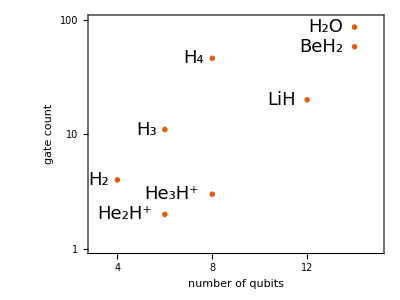

```mathematica
ListLogPlot[{gatesgrow},Joined->{False,True},
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"number of qubits","gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,24],PlotRange->{{3,15},{1,100}},PlotMarkers->"OpenMarkers",
AspectRatio->3/4,Background->White,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Range[4,14,2],Automatic}},GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/vqe-best-gates.pdf",%]
```

/home/cica/chemistry/img/vqe-best-gates.pdf

```mathematica
runsum=<|#->summary[#,data]&/@Keys@hamiltonians|>;
```

```mathematica
molecules=Keys@hamiltonians
```

{BeH2,LiH,H2O,H2,H3,H4,He2H,He3H}

Gate count: doubles, singles

```mathematica
Table[{k,ToString@CountGates[bestres[k][[1]]]},{k,Keys@hamiltonians}]//TableForm
```

BeH2 | {44, 14}
LiH | {14, 6}
H2O | {71, 15}
H2 | {4, 0}
H3 | {10, 1}
H4 | {40, 6}
He2H | {2, 0}
He3H | {2, 1}

Percentage of success

```mathematica
percentsucc=<|Table[k->ToString[IntegerPart[N[(succres[k]//Length),2]*10]]<>"%",{k,molecules}]|>
```

<|BeH2→80%,LiH→50%,H2O→30%,H2→100%,H3→100%,H4→60%,He2H→100%,He3H→100%|>

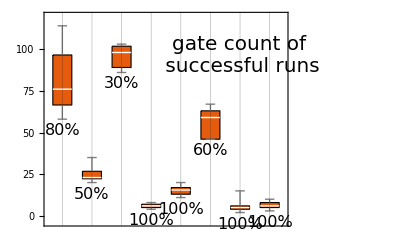

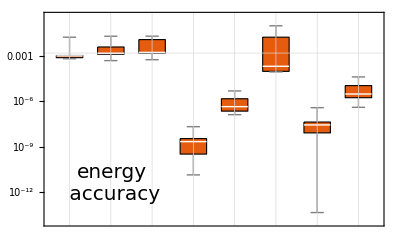

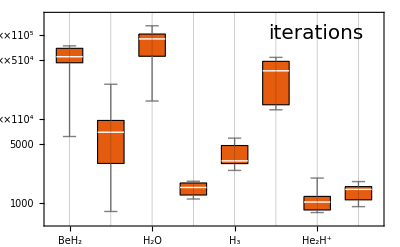

```mathematica
plotngates=BoxWhiskerChart[Values@Table[k->Select[runsum[k],#["ϵ"]<=chemacc&][[All,"ngates"]],{k,molecules}],FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],GridLines->{Range[Length@molecules],None},PlotTheme->"Scientific",GridLinesStyle->GrayLevel[0.1,0.3],Epilog->Text[Style["gate count of\n successful runs",20,FontFamily->"FreeSerif",Background->White],Scaled[{.8,.8}]],ImageSize->400,
ImagePadding->{{60,10},{0,10}},ChartLabels->Placed[Table[percentsucc[m],{m,molecules}],Below],LabelStyle->Directive[Black,16, FontFamily->"FreeSerif"]
]

plotacc=BoxWhiskerChart[Values@Table[k->runsum[k][[All,"ϵ"]],{k,molecules}],ScalingFunctions->"Log10",FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],GridLines->{Range[Length@molecules],{Log10@chemacc}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]},PlotTheme->"Scientific",Epilog->Text[Style["energy\n accuracy",20,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.2}]],ImageSize->400,
ImagePadding->{{60,10},{0,0}}
]

plotfev=BoxWhiskerChart[Values@Table[k->runsum[k][[All,"nfev"]],{k,molecules}],ScalingFunctions->"Log10",FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[Table[labels[m],{m,molecules}],Axis,Rotate[#,30Degree]&],GridLines->{Range[Length@molecules],None},PlotTheme->"Scientific",GridLinesStyle->GrayLevel[0.1,0.3],Epilog->Text[Style["iterations",20,FontFamily->"FreeSerif",Background->White],Scaled[{.8,.9}]],ImageSize->400,
ImagePadding->{{60,10},{44,0}}
]
```

```mathematica
whiskers=Column[{plotngates,plotacc,plotfev},Spacings->-0.1];
```

```mathematica
Export["/home/cica/chemistry/img/whiskers.pdf",whiskers]
```

/home/cica/chemistry/img/whiskers.pdf

### Rounding the results: module ?roundingAnsatzIterate

```mathematica
succres=<| Table[mol->GetSuccData[mol] ,{mol,Keys@hamiltonians}]|>;
```

```mathematica
ClearAll[roundingAnsatzIterate]
roundingAnsatzIterate::usage="roundingAnsatzIterate[ansatz,θvars,ansatzinit,hamiltonian,ψ,ψwork,accuracy,maxfrac]. Iterate the rounding to π/j, where j is increased up to maxfrac. Iteration stops when energy difference is less than the accuracy.";
roundingAnsatzIterate[ansatz_,θvars_,ansatzinit_,hamiltonian_,ψ_,ψwork_,accuracy_,maxfrac_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,frac,newcost,cost}
,
newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;
frac=1;
While[frac<= maxfrac,
θvarsnew=<|Table[  (k/.newkeys)->Round[θvars[k] ,π/frac] ,{k,Keys@θvars}] |>;
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,ansatznew]/.θvarsnew];
newcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
If[(newcost-cost)<=accuracy,Break[]];
frac++;
];
{ansatznew/.θvarsnew,newcost}
]
```

```mathematica
bestres=<|Table[
mol->succres[mol][[First@Ordering[Length[#[[1]]]&/@succres[mol],1]]],{mol,Keys@hamiltonians}]|>;
```

maxfrac=200;
accuracy=10^-4;
roundRes=Table[
molecule->
With[{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[X_i,{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
result=bestres[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
{ansatz,newcost}=roundingAnsatzIterate[result[[1]],result[[2]],ansatzinit,hamiltonian,ψ,ψwork,accuracy,maxfrac];
Print["Best result of ",molecule," has ϵ=",newcost-groundstate];
{ansatz,newcost,newcost-groundstate,Length@ansatz}
],{molecule,Keys@hamiltonians}];

Best result of BeH2 has ϵ=0.00131873

Best result of LiH has ϵ=0.00151079

Best result of H2O has ϵ=0.00179457

Best result of H2 has ϵ=0.0000129511

Best result of H3 has ϵ=0.0000123006

Best result of H4 has ϵ=0.000192186

Best result of He2H has ϵ=1.23311×10^-6

Best result of He3H has ϵ=0.0000447107

roundRes = <|roundRes|>;

DumpSave["roundRes.mx", roundRes];

```mathematica
roundRes<<"roundRes.mx"
```

Null roundRes

------ Molecule BeH2 ϵ=0.00131873 ngates=58 ------

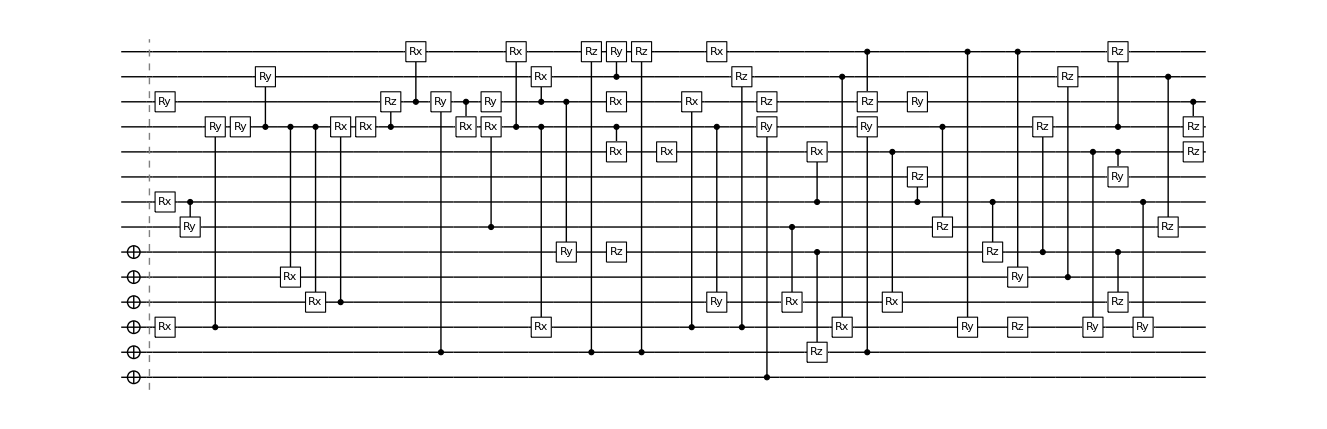

{Rx_7[(7 π)/200],Ry_11[(103 π)/200],Rx_2[(13 π)/200],C_7[Ry_6[π]],C_2[Ry_10[π]],Ry_10[-π],C_10[Ry_12[π]],C_10[Rx_4[π]],C_10[Rx_3[π]],C_3[Rx_10[-(33 π)/20]],Rx_10[(41 π)/25],C_10[Rz_11[(97 π)/100]],C_11[Rx_13[(3 π)/40]],C_1[Ry_11[-(147 π)/100]],C_11[Rx_10[-(9 π)/200]],Ry_11[(193 π)/200],C_6[Rx_10[π/20]],C_10[Rx_13[-(119 π)/50]],C_11[Rx_12[-π]],C_10[Rx_2[-π]],C_11[Ry_5[-π]],C_1[Rz_13[(113 π)/200]],C_10[Rx_9[-π/40]],C_12[Ry_13[-(17 π)/50]],Rx_11[π/2],Rz_5[-(23 π)/40],C_1[Rz_13[-(113 π)/200]],Rx_9[(7 π)/200],C_2[Rx_11[-π]],C_10[Ry_3[π]],Rx_13[-(7 π)/200],C_2[Rz_12[(79 π)/100]],Rz_11[-π/2],C_0[Ry_10[-(37 π)/50]],C_6[Rx_3[π]],C_5[Rz_1[-π]],C_7[Rx_9[-(7 π)/200]],C_12[Rx_2[-π]],C_1[Ry_10[(37 π)/50]],C_13[Rz_11[-π]],C_9[Rx_3[π]],C_7[Rz_8[(4 π)/5]],Ry_11[-π/2],C_10[Rz_6[(59 π)/100]],C_13[Ry_2[-π]],C_7[Rz_5[(19 π)/50]],C_13[Ry_4[π]],Rz_2[(49 π)/200],C_5[Rz_10[-(17 π)/20]],C_4[Rz_12[(21 π)/40]],C_9[Ry_2[-π]],C_5[Rz_3[-(21 π)/100]],C_10[Rz_13[(14 π)/25]],C_9[Ry_8[π]],C_7[Ry_2[-π]],C_12[Rz_6[(63 π)/100]],C_11[Rz_10[(23 π)/200]],Rz_9[-(21 π)/100]}

------ Molecule LiH ϵ=0.00151079 ngates=20 ------

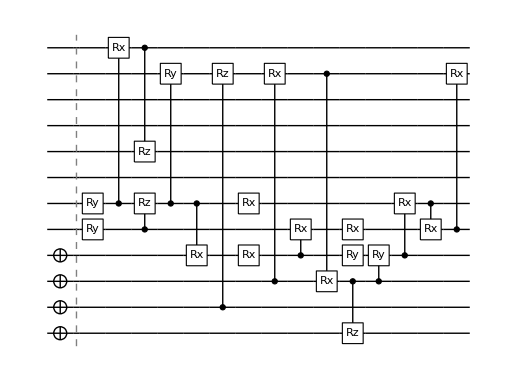

{Ry_4[-(27 π)/200],Ry_5[(2 π)/25],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-(141 π)/200]],C_5[Ry_10[(24 π)/25]],C_5[Rx_3[π/40]],C_1[Rz_10[(16 π)/25]],Rx_5[π],Rx_3[-π/40],C_2[Rx_10[-(9 π)/200]],C_3[Rx_4[-(31 π)/100]],C_10[Rx_2[-π]],Rx_4[(9 π)/20],Ry_3[π],C_2[Rz_0[(197 π)/200]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-(8 π)/25]],C_4[Rx_10[π]]}

------ Molecule H2O ϵ=0.00179457 ngates=86 ------

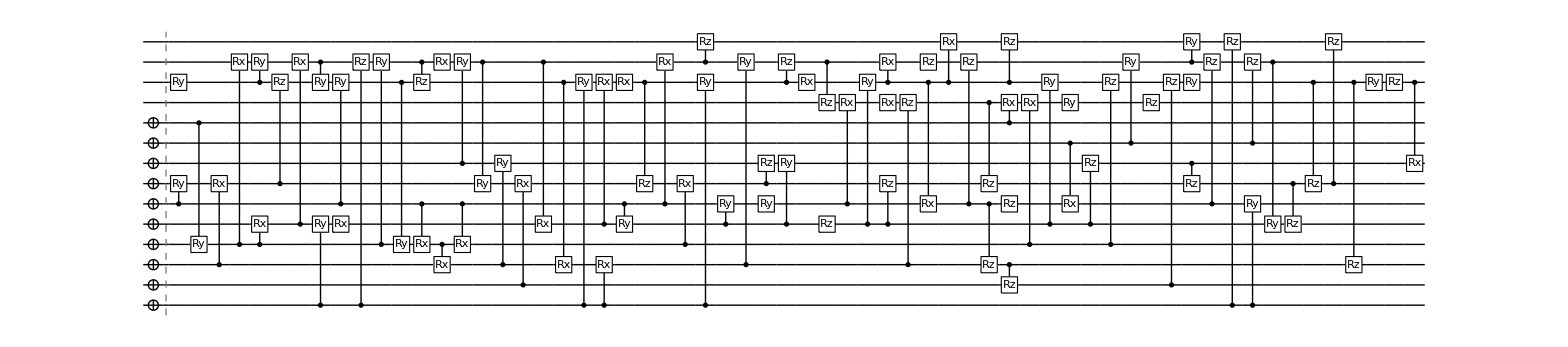

{Ry_11[(3 π)/2],C_5[Ry_6[-π/25]],C_9[Ry_3[-π/40]],C_2[Rx_6[-π/25]],C_3[Rx_12[(89 π)/100]],C_11[Ry_12[-(199 π)/200]],C_3[Rx_4[-(11 π)/100]],C_6[Rz_11[(103 π)/200]],C_4[Rx_12[-(29 π)/200]],C_12[Ry_11[(119 π)/100]],C_0[Ry_4[(19 π)/20]],Rx_4[(23 π)/25],C_5[Ry_11[-(123 π)/100]],C_0[Rz_12[(11 π)/100]],C_3[Ry_12[(3 π)/8]],C_11[Ry_3[(49 π)/50]],C_12[Rz_11[(14 π)/25]],C_5[Rx_3[-(51 π)/50]],Rx_12[(13 π)/40],C_3[Rx_2[π]],C_7[Ry_12[-(53 π)/200]],C_5[Rx_3[π]],C_12[Ry_6[(21 π)/10]],C_2[Ry_7[π]],C_1[Rx_6[(3 π)/100]],C_12[Rx_4[(11 π)/10]],C_11[Rx_2[-(193 π)/200]],C_0[Ry_11[π]],C_4[Rx_11[(13 π)/50]],C_0[Rx_2[-π/50]],C_5[Ry_4[-(11 π)/200]],Rx_11[(47 π)/200],C_11[Rz_6[-(49 π)/50]],C_5[Rx_12[-(43 π)/100]],C_3[Rx_6[(3 π)/100]],C_0[Ry_11[π/5]],C_12[Rz_13[(203 π)/100]],C_4[Ry_5[-π]],C_2[Ry_12[(79 π)/200]],Ry_5[π],C_6[Rz_7[(3 π)/4]],C_4[Ry_7[π]],C_11[Rz_12[-(3 π)/40]],Rx_11[(49 π)/50],C_12[Rz_10[(59 π)/50]],Rz_4[-(337 π)/200],C_5[Rx_10[-π]],C_4[Ry_11[-(61 π)/200]],Rx_10[-π/2],C_11[Rx_12[-(107 π)/200]],C_4[Rz_6[-(9 π)/25]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[(17 π)/200],C_11[Rx_13[-π]],C_5[Rz_12[-(409 π)/200]],C_10[Rz_6[π]],C_5[Rz_2[-(53 π)/100]],C_9[Rx_10[(9 π)/20]],C_11[Rz_13[(77 π)/50]],C_2[Rz_1[-(243 π)/200]],Rz_5[(217 π)/200],C_3[Rx_10[-(57 π)/100]],C_4[Ry_11[-(199 π)/200]],C_8[Rx_5[π/2]],Ry_10[π/2],C_4[Rz_7[(193 π)/200]],C_3[Rz_11[(14 π)/25]],C_8[Ry_12[(19 π)/40]],Rz_10[-(147 π)/100],C_1[Rz_11[(87 π)/100]],C_7[Rz_6[-(73 π)/100]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],C_0[Rz_13[-(361 π)/200]],C_8[Rz_12[-(13 π)/5]],C_0[Ry_5[-π/2]],C_12[Ry_4[-3 π]],C_6[Rz_4[(57 π)/100]],C_11[Rz_6[(197 π)/200]],C_6[Rz_13[(51 π)/100]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-(17 π)/200],C_11[Rx_7[-π]]}

------ Molecule H2 ϵ=0.0000129511 ngates=4 ------

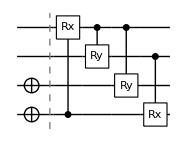

{C_0[Rx_3[-(7 π)/100]],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

------ Molecule H3 ϵ=0.0000123006 ngates=11 ------

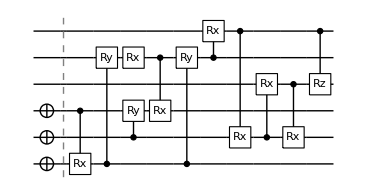

{C_2[Rx_0[(41 π)/200]],C_0[Ry_4[-(29 π)/200]],C_1[Ry_2[-π]],Rx_4[-π],C_4[Rx_2[π]],C_0[Ry_4[π]],C_4[Rx_5[-π]],C_5[Rx_1[-π]],C_1[Rx_3[-π/25]],C_3[Rx_1[π]],C_5[Rz_3[π]]}

------ Molecule H4 ϵ=0.000192186 ngates=46 ------

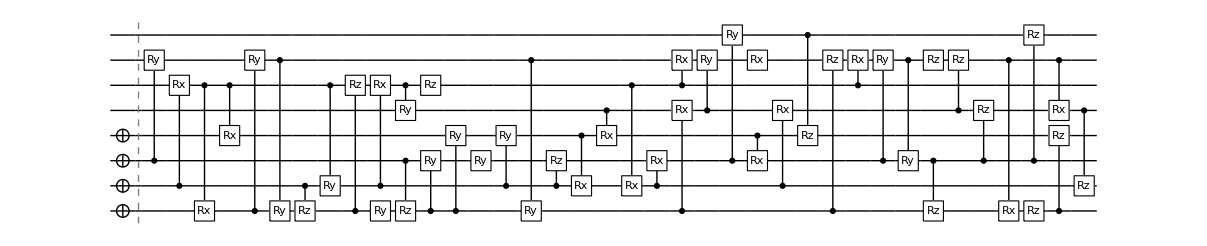

{C_2[Ry_6[-(319 π)/200]],C_1[Rx_5[-(29 π)/200]],C_5[Rx_0[-(139 π)/200]],C_5[Rx_3[-π]],C_0[Ry_6[-(7 π)/20]],C_6[Ry_0[(17 π)/25]],C_1[Rz_0[(18 π)/25]],C_5[Ry_1[π]],C_0[Rz_5[-(8 π)/25]],C_1[Rx_5[-(47 π)/200]],Ry_0[-π/8],C_5[Ry_4[π]],C_2[Rz_0[-(81 π)/100]],C_0[Ry_2[-π]],Rz_5[(27 π)/50],C_0[Ry_3[-π]],Ry_2[π],C_1[Ry_3[π]],C_6[Ry_0[(31 π)/200]],C_1[Rz_2[(79 π)/100]],C_3[Rx_1[(27 π)/200]],C_4[Rx_3[π]],C_5[Rx_1[-(51 π)/200]],C_1[Rx_2[-π]],C_0[Rx_4[π]],C_5[Rx_6[(139 π)/200]],C_4[Ry_6[(39 π)/40]],C_2[Ry_7[-π]],Rx_6[(47 π)/100],C_3[Rx_2[π]],C_1[Rx_4[-π]],C_7[Rz_3[(219 π)/100]],C_0[Rz_6[(351 π)/100]],C_5[Rx_6[(161 π)/200]],C_2[Ry_6[-(99 π)/200]],C_6[Ry_2[-π]],C_2[Rz_0[(131 π)/200]],Rz_6[(149 π)/200],C_4[Rz_6[-(131 π)/200]],C_2[Rz_4[-(41 π)/200]],C_6[Rx_0[π]],Rz_0[(36 π)/25],C_2[Rz_7[-(51 π)/200]],C_6[Rx_4[π]],C_0[Rz_3[(43 π)/200]],C_4[Rz_1[(137 π)/50]]}

------ Molecule He2H ϵ=1.23311×10^-6 ngates=2 ------

-Graphics-

{C_3[Rx_5[-(9 π)/200]],C_5[Rx_1[π]]}

------ Molecule He3H ϵ=0.0000447107 ngates=3 ------

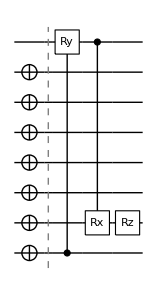

{C_0[Ry_7[-(9 π)/200]],C_7[Rx_1[π]],Rz_1[π/2]}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
Print["------ Molecule ",k," ϵ=",roundRes[k][[3]]," ngates=",Length@roundRes[k][[1]]," ------"];
Print[DrawCircuit[{Subscript[X, #]&/@Range[0,occupations[k]-1],roundRes[k][[1]]}]];
Print[roundRes[k][[1]]];
,{k,Keys@hamiltonians}]
```

### Rounding θ, if possible: module ?roundingAnsatzSoft

```mathematica
ClearAll[roundingAnsatzSoft]
roundingAsatzSoft::usage="roundingAnsatzSoft[ansatz,θvars,ansatzinit,hamiltonian,ψ,ψwork,fraction_of_π,decimal,θerr]. Rounding to multiplication of fraction if rounding difference is less than θerr, otherwise rounded to dec decimals.";
roundingAnsatzSoft[ansatz_,θvars_,ansatzinit_,hamiltonian_,ψ_,ψwork_,fraction_,decimal_,θerr_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,newcost,cost,roundθ}
,
newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;

θvarsnew=<|Table[  
roundθ=Round[θvars[k] ,π/fraction] ;
(k/.newkeys)->If[Abs[roundθ-θvars[k]]<=θerr,roundθ,Round[θvars[k],N[1.0*10^-decimal]]] 
,{k,Keys@θvars}] 
|>;
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,ansatznew]/.θvarsnew];
newcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];

{ansatznew/.θvarsnew,newcost}
]
```

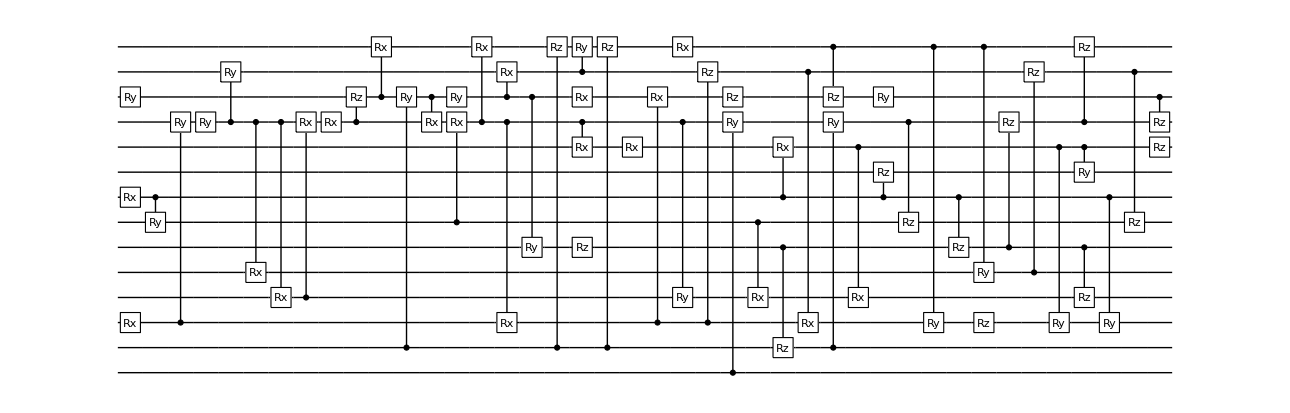
Best result of BeH2 has ϵ_new=0.0010995874444343912, ϵ_before=0.0010787209879961068
-Graphics-
{Rx_7[0.1],Ry_11[1.61],Rx_2[0.21],C_7[Ry_6[π]],C_2[Ry_10[π]],Ry_10[-π],C_10[Ry_12[π]],C_10[Rx_4[π]],C_10[Rx_3[π]],C_3[Rx_10[-5.18]],Rx_10[5.16],C_10[Rz_11[3.05]],C_11[Rx_13[0.23]],C_1[Ry_11[-4.62]],C_11[Rx_10[-0.15]],Ry_11[3.04],C_6[Rx_10[0.15]],C_10[Rx_13[-7.48]],C_11[Rx_12[-π]],C_10[Rx_2[-π]],C_11[Ry_5[-π]],C_1[Rz_13[1.78]],C_10[Rx_9[-0.08]],C_12[Ry_13[-1.07]],Rx_11[π/2],Rz_5[-1.81],C_1[Rz_13[-1.78]],Rx_9[0.1],C_2[Rx_11[-π]],C_10[Ry_3[π]],Rx_13[-0.12],C_2[Rz_12[2.48]],Rz_11[-π/2],C_0[Ry_10[-2.32]],C_6[Rx_3[π]],C_5[Rz_1[-π]],C_7[Rx_9[-0.1]],C_12[Rx_2[-π]],C_1[Ry_10[2.32]],C_13[Rz_11[-π]],C_9[Rx_3[π]],C_7[Rz_8[2.51]],Ry_11[-π/2],C_10[Rz_6[1.86]],C_13[Ry_2[-π]],C_7[Rz_5[1.19]],C_13[Ry_4[π]],Rz_2[0.76],C_5[Rz_10[-2.67]],C_4[Rz_12[1.65]],C_9[Ry_2[-π]],C_5[Rz_3[-0.66]],C_10[Rz_13[1.76]],C_9[Ry_8[π]],C_7[Ry_2[-π]],C_12[Rz_6[1.98]],C_11[Rz_10[0.37]],Rz_9[-0.66]}

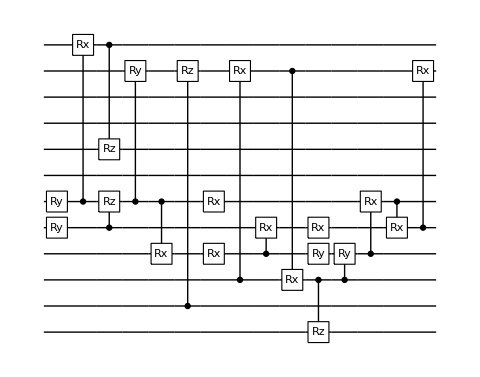
Best result of LiH has ϵ_new=0.0014445519822849917, ϵ_before=0.0014426249126735513
-Graphics-
{Ry_4[-0.43],Ry_5[0.26],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.21]],C_5[Ry_10[3.01]],C_5[Rx_3[0.08]],C_1[Rz_10[2.01]],Rx_5[π],Rx_3[-0.07],C_2[Rx_10[-0.14]],C_3[Rx_4[-0.98]],C_10[Rx_2[-π]],Rx_4[1.41],Ry_3[π],C_2[Rz_0[3.1]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.]],C_4[Rx_10[π]]}

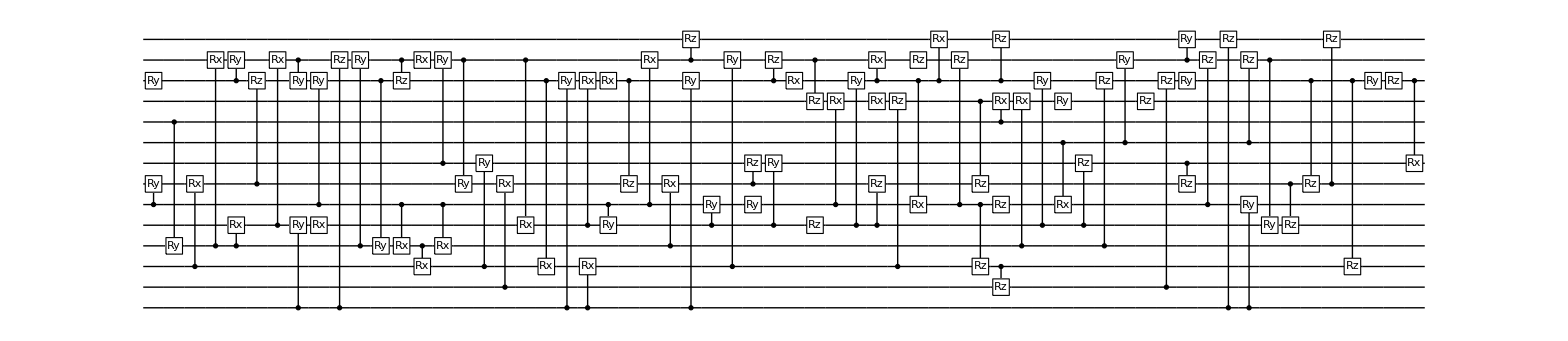
Best result of H2O has ϵ_new=0.0016979349874475247, ϵ_before=0.0015334962047148792
-Graphics-
{Ry_11[(3 π)/2],C_5[Ry_6[-0.13]],C_9[Ry_3[-0.09]],C_2[Rx_6[-0.13]],C_3[Rx_12[2.79]],C_11[Ry_12[-3.13]],C_3[Rx_4[-0.34]],C_6[Rz_11[1.62]],C_4[Rx_12[-0.45]],C_12[Ry_11[3.74]],C_0[Ry_4[2.99]],Rx_4[2.9],C_5[Ry_11[-3.86]],C_0[Rz_12[0.35]],C_3[Ry_12[1.17]],C_11[Ry_3[3.07]],C_12[Rz_11[1.76]],C_5[Rx_3[-3.2]],Rx_12[1.02],C_3[Rx_2[π]],C_7[Ry_12[-0.83]],C_5[Rx_3[π]],C_12[Ry_6[6.59]],C_2[Ry_7[π]],C_1[Rx_6[0.09]],C_12[Rx_4[3.46]],C_11[Rx_2[-3.04]],C_0[Ry_11[π]],C_4[Rx_11[0.82]],C_0[Rx_2[-0.07]],C_5[Ry_4[-0.17]],Rx_11[0.73],C_11[Rz_6[-3.08]],C_5[Rx_12[-1.35]],C_3[Rx_6[0.1]],C_0[Ry_11[0.63]],C_12[Rz_13[6.38]],C_4[Ry_5[-π]],C_2[Ry_12[1.24]],Ry_5[π],C_6[Rz_7[2.35]],C_4[Ry_7[π]],C_11[Rz_12[-0.23]],Rx_11[3.07],C_12[Rz_10[3.7]],Rz_4[-5.3],C_5[Rx_10[-π]],C_4[Ry_11[-0.96]],Rx_10[-π/2],C_11[Rx_12[-1.68]],C_4[Rz_6[-1.14]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[0.26],C_11[Rx_13[-π]],C_5[Rz_12[-6.42]],C_10[Rz_6[π]],C_5[Rz_2[-1.67]],C_9[Rx_10[1.42]],C_11[Rz_13[4.84]],C_2[Rz_1[-3.82]],Rz_5[3.41],C_3[Rx_10[-1.79]],C_4[Ry_11[-π]],C_8[Rx_5[π/2]],Ry_10[π/2],C_4[Rz_7[3.03]],C_3[Rz_11[1.76]],C_8[Ry_12[1.49]],Rz_10[-4.62],C_1[Rz_11[2.74]],C_7[Rz_6[-2.29]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],C_0[Rz_13[-5.66]],C_8[Rz_12[-8.17]],C_0[Ry_5[-π/2]],C_12[Ry_4[-3 π]],C_6[Rz_4[1.79]],C_11[Rz_6[3.09]],C_6[Rz_13[1.6]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-0.27],C_11[Rx_7[-π]]}

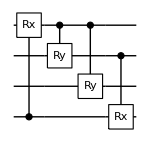
Best result of H2 has ϵ_new=7.965721122271674e-6, ϵ_before=1.361399881716352e-11
-Graphics-
{C_0[Rx_3[-0.23]],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

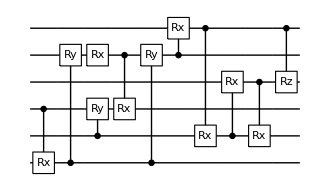
Best result of H3 has ϵ_new=8.44177737047147e-7, ϵ_before=6.60757461190542e-7
-Graphics-
{C_2[Rx_0[0.64]],C_0[Ry_4[-0.45]],C_1[Ry_2[-π]],Rx_4[-π],C_4[Rx_2[π]],C_0[Ry_4[π]],C_4[Rx_5[-π]],C_5[Rx_1[-π]],C_1[Rx_3[-0.13]],C_3[Rx_1[π]],C_5[Rz_3[π]]}

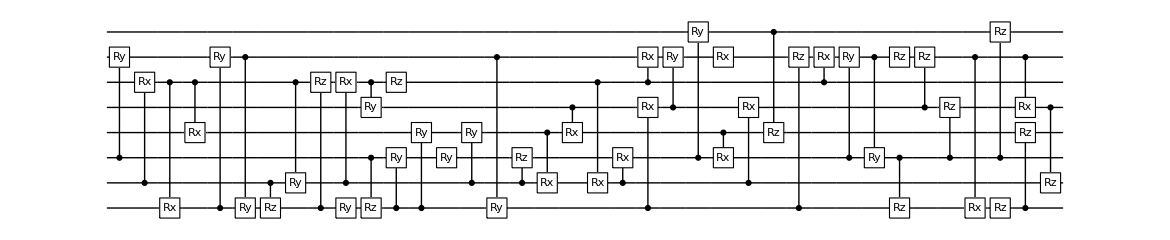
Best result of H4 has ϵ_new=0.0001367896658350798, ϵ_before=0.00010732297367055388
-Graphics-
{C_2[Ry_6[-5.01]],C_1[Rx_5[-0.45]],C_5[Rx_0[-2.18]],C_5[Rx_3[-π]],C_0[Ry_6[-1.1]],C_6[Ry_0[2.14]],C_1[Rz_0[2.26]],C_5[Ry_1[π]],C_0[Rz_5[-1.01]],C_1[Rx_5[-0.75]],Ry_0[-0.4],C_5[Ry_4[π]],C_2[Rz_0[-2.54]],C_0[Ry_2[-π]],Rz_5[1.69],C_0[Ry_3[-π]],Ry_2[π],C_1[Ry_3[π]],C_6[Ry_0[0.48]],C_1[Rz_2[2.49]],C_3[Rx_1[0.42]],C_4[Rx_3[π]],C_5[Rx_1[-0.8]],C_1[Rx_2[-π]],C_0[Rx_4[π]],C_5[Rx_6[2.19]],C_4[Ry_6[3.06]],C_2[Ry_7[-π]],Rx_6[1.48],C_3[Rx_2[π]],C_1[Rx_4[-π]],C_7[Rz_3[6.88]],C_0[Rz_6[11.03]],C_5[Rx_6[2.53]],C_2[Ry_6[-1.55]],C_6[Ry_2[-π]],C_2[Rz_0[2.06]],Rz_6[2.34],C_4[Rz_6[-2.07]],C_2[Rz_4[-0.64]],C_6[Rx_0[π]],Rz_0[4.53],C_2[Rz_7[-0.81]],C_6[Rx_4[π]],C_0[Rz_3[0.68]],C_4[Rz_1[8.6]]}

Best result of He2H has ϵ_new=3.383765386999471e-6, ϵ_before=4.3520742565306136e-14
-Graphics-
{C_3[Rx_5[-0.14]],C_5[Rx_1[π]]}

Best result of He3H has ϵ_new=0.000047777493634271195, ϵ_before=0.00004177900040502891
-Graphics-
{C_0[Ry_7[-0.14]],C_7[Rx_1[π]],Rz_1[π/2]}

```mathematica
accuracy=10^-2;
fraction=2;
decimal=2;
roundsoftRes=<|Table[
molecule->
With[{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
result=bestres[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,result[[1]]]/.result[[2]]];
oldcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];

{ansatz,newcost}=roundingAnsatzSoft[result[[1]],result[[2]],ansatzinit,hamiltonian,ψ,ψwork,fraction,decimal,accuracy];
Print@Column@{"Best result of "<>molecule<>" has ϵ_new="<>ToString[newcost-groundstate,FortranForm]<>", ϵ_before="<>ToString[oldcost-groundstate,FortranForm],DrawCircuit[ansatz,nqubits],ansatz};
{ansatz,newcost,newcost-groundstate,Length@ansatz}
],{molecule,Keys@hamiltonians}]|>;
```

### Print some ansatze to quantikz format

```mathematica
DumpSave["roundsoftRes.mx", roundsoftRes];
```

```mathematica
roundsoftRes<<"roundsoftRes.mx"
```

<|BeH2→{{Null Rx_7[0.1],Null Ry_11[1.61],Null Rx_2[0.21],Null C_7[Ry_6[π]],Null C_2[Ry_10[π]],Null Ry_10[-π],Null C_10[Ry_12[π]],Null C_10[Rx_4[π]],Null C_10[Rx_3[π]],Null C_3[Rx_10[-5.18]],Null Rx_10[5.16],Null C_10[Rz_11[3.05]],Null C_11[Rx_13[0.23]],Null C_1[Ry_11[-4.62]],Null C_11[Rx_10[-0.15]],Null Ry_11[3.04],Null C_6[Rx_10[0.15]],Null C_10[Rx_13[-7.48]],Null C_11[Rx_12[-π]],Null C_10[Rx_2[-π]],Null C_11[Ry_5[-π]],Null C_1[Rz_13[1.78]],Null C_10[Rx_9[-0.08]],Null C_12[Ry_13[-1.07]],Null Rx_11[π/2],Null Rz_5[-1.81],Null C_1[Rz_13[-1.78]],Null Rx_9[0.1],Null C_2[Rx_11[-π]],Null C_10[Ry_3[π]],Null Rx_13[-0.12],Null C_2[Rz_12[2.48]],Null Rz_11[-π/2],Null C_0[Ry_10[-2.32]],Null C_6[Rx_3[π]],Null C_5[Rz_1[-π]],Null C_7[Rx_9[-0.1]],Null C_12[Rx_2[-π]],Null C_1[Ry_10[2.32]],Null C_13[Rz_11[-π]],Null C_9[Rx_3[π]],Null C_7[Rz_8[2.51]],Null Ry_11[-π/2],Null C_10[Rz_6[1.86]],Null C_13[Ry_2[-π]],Null C_7[Rz_5[1.19]],Null C_13[Ry_4[π]],Null Rz_2[0.76],Null C_5[Rz_10[-2.67]],Null C_4[Rz_12[1.65]],Null C_9[Ry_2[-π]],Null C_5[Rz_3[-0.66]],Null C_10[Rz_13[1.76]],Null C_9[Ry_8[π]],Null C_7[Ry_2[-π]],Null C_12[Rz_6[1.98]],Null C_11[Rz_10[0.37]],Null Rz_9[-0.66]},-15.5941 Null,0.00109959 Null,58 Null},LiH→{{Null Ry_4[-0.43],Null Ry_5[0.26],Null C_5[Rx_11[π]],Null C_4[Rz_5[π]],Null C_11[Rz_7[-2.21]],Null C_5[Ry_10[3.01]],Null C_5[Rx_3[0.08]],Null C_1[Rz_10[2.01]],Null Rx_5[π],Null Rx_3[-0.07],Null C_2[Rx_10[-0.14]],Null C_3[Rx_4[-0.98]],Null C_10[Rx_2[-π]],Null Rx_4[1.41],Null Ry_3[π],Null C_2[Rz_0[3.1]],Null C_2[Ry_3[-π]],Null C_3[Rx_5[-π]],Null C_5[Rx_4[-1.]],Null C_4[Rx_10[π]]},-7.88062 Null,0.00144455 Null,20 Null},H2O→{{Null Ry_11[(3 π)/2],Null C_5[Ry_6[-0.13]],Null C_9[Ry_3[-0.09]],Null C_2[Rx_6[-0.13]],Null C_3[Rx_12[2.79]],Null C_11[Ry_12[-3.13]],Null C_3[Rx_4[-0.34]],Null C_6[Rz_11[1.62]],Null C_4[Rx_12[-0.45]],Null C_12[Ry_11[3.74]],Null C_0[Ry_4[2.99]],Null Rx_4[2.9],Null C_5[Ry_11[-3.86]],Null C_0[Rz_12[0.35]],Null C_3[Ry_12[1.17]],Null C_11[Ry_3[3.07]],Null C_12[Rz_11[1.76]],Null C_5[Rx_3[-3.2]],Null Rx_12[1.02],Null C_3[Rx_2[π]],Null C_7[Ry_12[-0.83]],Null C_5[Rx_3[π]],Null C_12[Ry_6[6.59]],Null C_2[Ry_7[π]],Null C_1[Rx_6[0.09]],Null C_12[Rx_4[3.46]],Null C_11[Rx_2[-3.04]],Null C_0[Ry_11[π]],Null C_4[Rx_11[0.82]],Null C_0[Rx_2[-0.07]],Null C_5[Ry_4[-0.17]],Null Rx_11[0.73],Null C_11[Rz_6[-3.08]],Null C_5[Rx_12[-1.35]],Null C_3[Rx_6[0.1]],Null C_0[Ry_11[0.63]],Null C_12[Rz_13[6.38]],Null C_4[Ry_5[-π]],Null C_2[Ry_12[1.24]],Null Ry_5[π],Null C_6[Rz_7[2.35]],Null C_4[Ry_7[π]],Null C_11[Rz_12[-0.23]],Null Rx_11[3.07],Null C_12[Rz_10[3.7]],Null Rz_4[-5.3],Null C_5[Rx_10[-π]],Null C_4[Ry_11[-0.96]],Null Rx_10[-π/2],Null C_11[Rx_12[-1.68]],Null C_4[Rz_6[-1.14]],Null C_2[Rz_10[π]],Null C_11[Rx_5[π]],Null Rz_12[0.26],Null C_11[Rx_13[-π]],Null C_5[Rz_12[-6.42]],Null C_10[Rz_6[π]],Null C_5[Rz_2[-1.67]],Null C_9[Rx_10[1.42]],Null C_11[Rz_13[4.84]],Null C_2[Rz_1[-3.82]],Null Rz_5[3.41],Null C_3[Rx_10[-1.79]],Null C_4[Ry_11[-π]],Null C_8[Rx_5[π/2]],Null Ry_10[π/2],Null C_4[Rz_7[3.03]],Null C_3[Rz_11[1.76]],Null C_8[Ry_12[1.49]],Null Rz_10[-4.62],Null C_1[Rz_11[2.74]],Null C_7[Rz_6[-2.29]],Null C_12[Ry_13[-π]],Null Ry_11[π/2],Null C_5[Rz_12[-π]],Null C_0[Rz_13[-5.66]],Null C_8[Rz_12[-8.17]],Null C_0[Ry_5[-π/2]],Null C_12[Ry_4[-3 π]],Null C_6[Rz_4[1.79]],Null C_11[Rz_6[3.09]],Null C_6[Rz_13[1.6]],Null C_11[Rz_2[π]],Null Ry_11[-π/2],Null Rz_11[-0.27],Null C_11[Rx_7[-π]]},-75.0123 Null,0.00169793 Null,86 Null},H2→{{Null C_0[Rx_3[-0.23]],Null C_3[Ry_2[-π]],Null C_3[Ry_1[-π]],Null C_2[Rx_0[π]]},-1.13728 Null,7.96572×10^-6 Null,4 Null},H3→{{Null C_2[Rx_0[0.64]],Null C_0[Ry_4[-0.45]],Null C_1[Ry_2[-π]],Null Rx_4[-π],Null C_4[Rx_2[π]],Null C_0[Ry_4[π]],Null C_4[Rx_5[-π]],Null C_5[Rx_1[-π]],Null C_1[Rx_3[-0.13]],Null C_3[Rx_1[π]],Null C_5[Rz_3[π]]},-1.41989 Null,8.44178×10^-7 Null,11 Null},H4→{{Null C_2[Ry_6[-5.01]],Null C_1[Rx_5[-0.45]],Null C_5[Rx_0[-2.18]],Null C_5[Rx_3[-π]],Null C_0[Ry_6[-1.1]],Null C_6[Ry_0[2.14]],Null C_1[Rz_0[2.26]],Null C_5[Ry_1[π]],Null C_0[Rz_5[-1.01]],Null C_1[Rx_5[-0.75]],Null Ry_0[-0.4],Null C_5[Ry_4[π]],Null C_2[Rz_0[-2.54]],Null C_0[Ry_2[-π]],Null Rz_5[1.69],Null C_0[Ry_3[-π]],Null Ry_2[π],Null C_1[Ry_3[π]],Null C_6[Ry_0[0.48]],Null C_1[Rz_2[2.49]],Null C_3[Rx_1[0.42]],Null C_4[Rx_3[π]],Null C_5[Rx_1[-0.8]],Null C_1[Rx_2[-π]],Null C_0[Rx_4[π]],Null C_5[Rx_6[2.19]],Null C_4[Ry_6[3.06]],Null C_2[Ry_7[-π]],Null Rx_6[1.48],Null C_3[Rx_2[π]],Null C_1[Rx_4[-π]],Null C_7[Rz_3[6.88]],Null C_0[Rz_6[11.03]],Null C_5[Rx_6[2.53]],Null C_2[Ry_6[-1.55]],Null C_6[Ry_2[-π]],Null C_2[Rz_0[2.06]],Null Rz_6[2.34],Null C_4[Rz_6[-2.07]],Null C_2[Rz_4[-0.64]],Null C_6[Rx_0[π]],Null Rz_0[4.53],Null C_2[Rz_7[-0.81]],Null C_6[Rx_4[π]],Null C_0[Rz_3[0.68]],Null C_4[Rz_1[8.6]]},-1.99601 Null,0.00013679 Null,46 Null},He2H→{{Null C_3[Rx_5[-0.14]],Null C_5[Rx_1[π]]},-5.76992 Null,3.38377×10^-6 Null,2 Null},He3H→{{Null C_0[Ry_7[-0.14]],Null C_7[Rx_1[π]],Null Rz_1[π/2]},-8.57527 Null,0.0000477775 Null,3 Null}|>

```mathematica
roundsoftRes["LiH"]
```

{{Ry_4[-0.43],Ry_5[0.26],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.21]],C_5[Ry_10[3.01]],C_5[Rx_3[0.08]],C_1[Rz_10[2.01]],Rx_5[π],Rx_3[-0.07],C_2[Rx_10[-0.14]],C_3[Rx_4[-0.98]],C_10[Rx_2[-π]],Rx_4[1.41],Ry_3[π],C_2[Rz_0[3.1]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.]],C_4[Rx_10[π]]},-7.88062,0.00144455,20}

```mathematica
inits=Join[ConstantArray[1,4],ConstantArray[0,8]]
```

{1,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/vqe/results

```mathematica
circ2quantikz[inits,roundsoftRes["LiH"][[1]],"lih.tex"]
```

circ2quantikz[{1,1,1,1,0,0,0,0,0,0,0,0},{Ry_4[-0.43],Ry_5[0.26],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.21]],C_5[Ry_10[3.01]],C_5[Rx_3[0.08]],C_1[Rz_10[2.01]],Rx_5[π],Rx_3[-0.07],C_2[Rx_10[-0.14]],C_3[Rx_4[-0.98]],C_10[Rx_2[-π]],Rx_4[1.41],Ry_3[π],C_2[Rz_0[3.1]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.]],C_4[Rx_10[π]]},lih.tex]

## Other people results

https://journals.aps.org/prxquantum/abstract/10.1103/PRXQuantum.2.020337
feature: fixed ansatz with permutation accounted which improves the accuracy

```mathematica
ansatz1[nq_,singles_,nlayer_]:=Table[
If[OddQ@layer,
Flatten@{Table[Subscript[s, q],{s,singles},{q,Range[0,nq-1]}],Table[Subscript[C, q-1][Subscript[X, q]],{q,Range[1,nq-1,2]}]}
,
Flatten@{Table[Subscript[s, q],{s,singles},{q,Range[1,nq-2]}],
Table[Subscript[C, i-1][Subscript[X, i]],{i,2,nq-2,2}]}
],{layer,nlayer}]
```

LiH

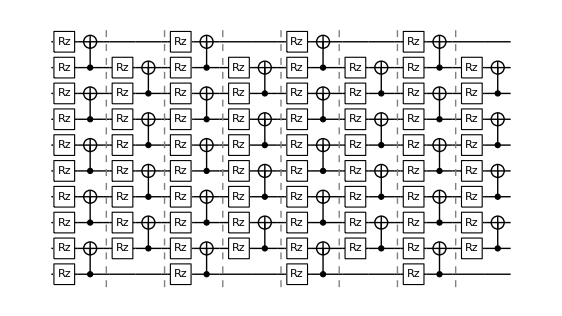

108

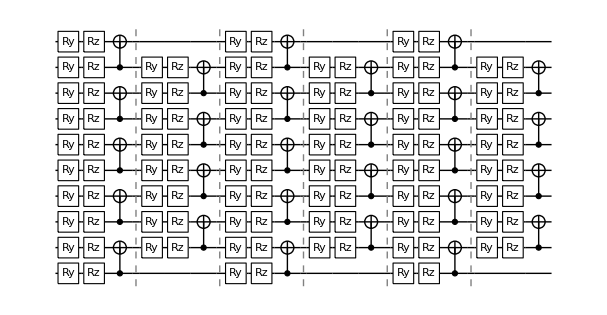

135

```mathematica
nq=10;
ansatz=ansatz1[nq,{Rz},8];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz

ansatz=ansatz1[nq,{Ry,Rz},6];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz
```

## Analysis on the hardness of the ground state: entanglement

Reference : https://arxiv.org/pdf/2111.03132.pdf,https://arxiv.org/pdf/2107.09155.pdf

```mathematica
VonNeumann[σ_]:=-Total[#*Log2[#]&/@σ]
```

```mathematica
GSInfo::usage="GSInfo[hamiltonian], return the analysis of the ground state of a hamiltonian."
GSInfo[hamiltonian_]:=Module[{eigvecs,eigs,gsidx,C,dim,u,σ,v,scoeff,vnentropy},
{eigs,eigvecs}=Eigensystem[CalcPauliSumMatrix[hamiltonian]];
gsidx=Ordering[eigs,1]//First;

(*reshape into bipartite state, then perfom SVD*)
dim=Sqrt@Length@eigvecs[[gsidx]];
C=ArrayReshape[eigvecs[[gsidx]],{dim,dim}];
{u,σ,v}=SingularValueDecomposition[C];
(*schmidt form*)
scoeff=Select[Diagonal@σ,#>0&];
vnentropy=VonNeumann[scoeff];
<|"eigvec"->eigvecs[[gsidx]], "eigval"->eigs[[gsidx]],"svd"->{u,σ,v},"srank"->Length@scoeff,"vnentropy"->vnentropy |>
]
```

GSInfo[hamiltonian], return the analysis of the ground state of a hamiltonian.

gsinfo = <|Table[
    Print["gather info on molecule ", mol];
    mol -> GSInfo[hamiltonians[mol][[1]]], {mol, hamiltonians // Keys}]
   |>;

gather info on molecule BeH2

gather info on molecule LiH

gather info on molecule H2O

gather info on molecule H2

gather info on molecule H3

gather info on molecule H4

gather info on molecule He2H

gather info on molecule He3H

```mathematica
gsinfo<<gsinfo.mx;
```

```mathematica
Table[gsinfo[m]["vnentropy"]=VonNeumann[Select[Diagonal@gsinfo[m]["svd"][[2]],#>0&]],{m,molecules}]
```

{2.00669,0.947925,1.97236,0.363812,1.28719,3.07336,0.276227,0.27742}

```mathematica
labelpos=<|"BeH2"->Left,"LiH"->Right,"H2O"->Right,"H2"->None,"H3"->Right,"H4"->Right,"He2H"->None,"He3H"->Above|>
```

<|BeH2→Left,LiH→Right,H2O→Right,H2→None,H3→Right,H4→Right,He2H→None,He3H→Above|>

```mathematica
srank=Table[Labeled[{N@Log2[gsinfo[mol]["srank"]],Around@(Length@#&/@succres[mol][[All,1]])},labels[mol],labelpos[mol],Background->None,FrameMargins->0],{mol,molecules}]/.{"He_3H^+":>"He_3H^+\nHe_2H^+\nH_2"}
```

{{5.67243,81.20.}BeH_2,{3.,25.6.}LiH,{4.64386,96.9.}H_2O,Labeled[{1.,6.01.5},H_2,None,Background→None,FrameMargins→0],{3.,15.42.9}H_3,{4.,57.9.}H_4,Labeled[{1.,6.4.},He_2H^+,None,Background→None,FrameMargins→0],Labeled[{1.,6.62.3},He_3H^+
He_2H^+
H_2,Above,Background→None,FrameMargins→0]}

```mathematica
vnentropy=Table[Labeled[{gsinfo[mol]["vnentropy"],bestres
[mol][[1]]//Length},labels[mol]],{mol,molecules}]
```

{{2.00669,58}BeH_2,{0.947925,20}LiH,{1.97236,86}H_2O,{0.363812,4}H_2,{1.28719,11}H_3,{3.07336,46}H_4,{0.276227,2}He_2H^+,{0.27742,3}He_3H^+}

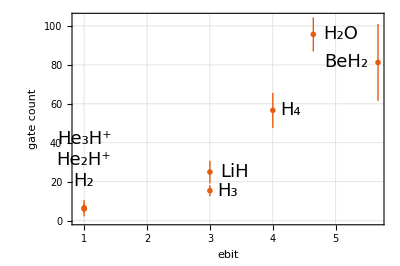

```mathematica
ListPlot[srank,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"ebit","gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,PlotMarkers->"OpenMarkers",
AspectRatio->2/3,Background->White,PlotTheme->"Scientific",GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/srank.pdf",%]
```

/home/cica/chemistry/img/srank.pdf

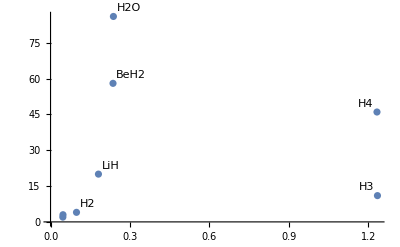

```mathematica
ListPlot[vnentropy]
```